-Graphics3D-

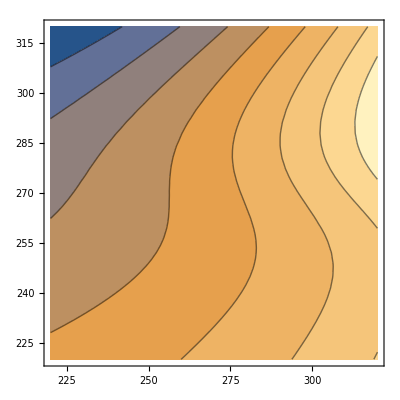

```mathematica
sigma = Quantity[5.67 *10^-8, "Watts"*("Meters"^-2)*("Kelvins"^-4)];
cp=Quantity[1000,"Joules"*("Kelvins"^-1)*("Kilograms"^-1)];
p=Quantity[10^5,"Pascals"];
g=Quantity[10,"Meters"*"Seconds"^-2];
c=(cp*p)/g;

tau = 0.68;

Plot3D[(1/c)(sigma*x^4(1-(0.45-0.25*Tanh[(y1-272)/23]))-(1/(1+tau))*sigma*y1^4),{x,220,320},{y1,220,320}]
ContourPlot[(1/c)(sigma*x^4(1-(0.45-0.25*Tanh[(y1-272)/23]))-(1/(1+tau))*sigma*y1^4),{x,220,320},{y1,220,320}]
```

#### Problem 2

```mathematica
N[Solve[ts == (1+tau1)^(1/4)*te && ts==270 &&te== 230,tau1]]
```

{{tau1→0.899082}}

```mathematica
volcanoCO2 = Quantity[24*10^12, "Grams"]
```

```mathematica
Solve[0.8990819786950447== 0.5 Log10[10*pCO2],pCO2]
```

{{pCO2→6.28296}}